```mathematica
0.5 x (1-x^2)
```

0.5 x (1-x^2)

```mathematica
Simplify[0.5 x (1-x^2)]
```

-0.5 x (-1.+x^2)

```mathematica
Expand[-0.5 x (-1.+x^2)]
```

0.5 x-0.5 x^3

```mathematica
f = 0.5 x (1-x^2)
```

0.5 x (1-x^2)

```mathematica
f
```

0.5 x (1-x^2)

```mathematica
df/dx
```

df/dx

```mathematica
D[df/dx, df]
```

1/dx

```mathematica
f
```

0.5 x (1-x^2)

```mathematica
D[(0.5 x (1-x^2)), x]
```

-1. x^2+0.5 (1-x^2)

```mathematica
Expand[-1. x^2+0.5 (1-x^2)]
```

0.5-1.5 x^2

```mathematica
J = mat{{0,1},{(0.5-1.5* x^2),-0.1}}
```

{{0,mat},{mat (0.5-1.5 x^2),-0.1 mat}}

```mathematica
J
```

{{0,mat},{mat (0.5-1.5 x^2),-0.1 mat}}

```mathematica
J = {{0,1},{(0.5-1.5* x^2),-0.1}}
```

{{0,1},{0.5-1.5 x^2,-0.1}}

```mathematica
J
```

{{0,1},{0.5-1.5 x^2,-0.1}}

```mathematica
J// MatrixForm
```

(0 | 1
0.5-1.5 x^2 | -0.1)

```mathematica
det(J)
```

{{0,det},{det (0.5-1.5 x^2),-0.1 det}}

```mathematica
Det[{{0,det},{det (0.5-1.5 x^2),-0.1 det}}]
```

0.-0.5 det^2+1.5 det^2 x^2

```mathematica
Manipulate[Plot[0.-0.5 det^2+1.5 det^2 x^2,{x,-8,8}],{det,-8,8}]
```

```mathematica
J// MatrixForm
```

(0 | 1
0.5-1.5 x^2 | -0.1)

(0 | 1
0.5-1.5 x^2 | -0.1)

```mathematica
Eigenvalues[{{0,1},{0.5-1.5 x^2,-0.1}}]
```

{0.5 (-0.1-√(2.01-6. x^2)),0.5 (-0.1+√(2.01-6. x^2))}

```mathematica
Det[{{0,1},{0.5-1.5 x^2,-0.1}}]
```

-0.5+1.5 x^2

```mathematica
Solve[-0.5+1.5 x^2==0,x]
```

{{x→-0.57735},{x→0.57735}}

```mathematica
Solve[0.5*(1-x^2)*x-0.1*x==0,x]
```

{{x→-0.894427},{x→0.},{x→0.894427}}

```mathematica
Solve[{y==0,0.5*(1-x^2)*x-0.1*y==0},{x,y}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→-1.,y→0.},{x→0.,y→0.},{x→1.,y→0.}}

```mathematica
J
```

{{0,1},{0.5-1.5 x^2,-0.1}}

```mathematica
Det[J]
```

-0.5+1.5 x^2

Fixed points

{{-7.31628,-7.31628,17.8427},{-1.12245,-1.12245,0.419962},{8.43873,8.43873,23.7374}}

-Graphics3D-

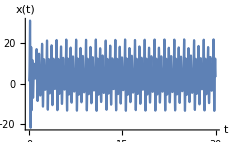
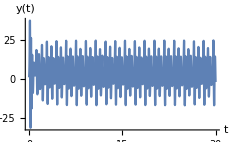
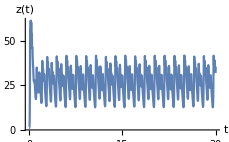

```mathematica
tmax=30;x0=1;y0=1;z0=1;
a=35;
b=3;
c=28;
m=23.1;

diffx=a (y-x);
diffy=(c-a) x-x z+c y+m;
diffz=x y-b z;

soln=NDSolve[{
x'[t]==Evaluate[diffx/.{x->x[t],y->y[t],z->z[t]}],
y'[t]==Evaluate[diffy/.{x->x[t],y->y[t],z->z[t]}],
z'[t]==Evaluate[diffz/.{x->x[t],y->y[t],z->z[t]}],
x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,tmax},MaxSteps->Infinity];
fixedpoints=Quiet[Solve[{diffx==0,diffy==0,diffz==0},{x,y,z}]];
Print[Style["Fixed points",18,Blue]]
coordinates={x,y,z}/.fixedpoints
Gfp=Graphics3D[{PointSize[0.03],Red,Point[coordinates]}];
pplot=ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.soln],{t,0,tmax},PlotPoints->1000,AxesLabel->{x[t],y[t],z[t]},PlotStyle->Thin,BoxRatios->{1,1,1},PlotRange->All,LabelStyle->18];
Show[pplot,Gfp]
Row[{Plot[Evaluate[x[t]/.soln],{t,0,tmax},AxesLabel-> {t,x[t]},PlotRange-> All,ImageSize->230,LabelStyle->18],
Plot[Evaluate[y[t]/.soln],{t,0,tmax},AxesLabel-> {t,y[t]},PlotRange-> All,ImageSize->230,LabelStyle->18],
Plot[Evaluate[z[t]/.soln],{t,0,tmax},AxesLabel-> {t,z[t]},PlotRange-> All,ImageSize->230,LabelStyle->18]}]
```